## Coupled Harmonic Oscillators

## Completed and Analyzed in class, February 18, 2025

This is the eighth notebook for you to complete.

### Coupled Oscillators — Formulas for the Accelerations

After all was said and done developing the theory, we were down to the following two simple equations for the accelerations,

a_1=-ω_0^2 x_1+ω_12^2(x_2-x_1)
 
a_2=-ω_0^2 x_2-ω_12^2(x_2-x_1)
 
where,
 
ω_0^2≡k/m

ω_12^2≡k_12/m

### Coupled Oscillators — Implementing the Accelerations

```mathematica
omega0=2Pi; (* this value is chosen so that the period with no coupling is 1 second *)
omega12=0.2 omega0; (* this value is chosen so that the coupling is weak *)

a1[x1_,x2_]:=-omega0^2 x1+omega12^2(x2-x1)
a2[x1_,x2_]:=-omega0^2 x2-omega12^2(x2-x1)
```

### Initial Conditions

Let’s let the spring be initially unstretched with no velocity and see what the external force does to it:

```mathematica
tInitial = 0.0;
tFinal = 60.0; 
initialx1=-0.5;
initialx2=0.0;
initialv1=0.0;
initialv2=0.0;
(* We have to decide how we are packing the time, the two positions, and the two *)
(* velocities into the initial conditions list. How about this as one of two obvious *)
(* choices (and I really can't see that one choice is any better than the other): *)
initialConditions={tInitial,initialx1,initialx2, initialv1,initialv2};
```

### Second-Order Runge-Kutta — Formulas for Two Particles

As on Exam 1, just to cut down on the work, let’s set λ=1/2, which simplifies the Second-Order Runge-Kutta formulas:

t_(i+1)=t_i+Δt

x_1^*=x_1(t_i)+v_1(t_i)·Δt/2

x_2^*=x_2(t_i)+v_2(t_i)·Δt/2

v_1(t_(i+1))=v_1(t_i)+a_1(x_1^*,x_2^*)·Δt

v_2(t_(i+1))=v_2(t_i)+a_2(x_1^*,x_2^*)·Δt

x_1(t_(i+1))=x_1(t_i)+ (v_1(t_i)+v_1(t_(i+1)))Δt/2

x_2(t_(i+1))=x_2(t_i)+ (v_2(t_i)+v_2(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementing the Formulas

```mathematica
steps = 12000;
deltaT = (tFinal - tInitial)/steps;

rungeKutta2[cc_]:= (
curTime=cc[[1]];
curx1=cc[[2]];
curx2=cc[[3]];
curv1=cc[[4]];
curv2=cc[[5]];
newTime=curTime+deltaT;
x1star=curx1+curv1 deltaT/2;
x2star=curx2+curv2 deltaT/2;
newv1=curv1+a1[x1star,x2star]deltaT;
newv2=curv2+a2[x1star,x2star]deltaT;
newx1=curx1+(curv1+newv1)deltaT/2;
newx2=curx2+(curv2+newv2)deltaT/2;
{newTime,newx1,newx2,newv1,newv2}
)
rungeKutta2[initialConditions]
```

{0.005,-0.499743,-9.8696×10^-6,0.102644,-0.00394784}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
rk2ResultsTransposed=Transpose[rk2Results];
times=rk2ResultsTransposed[[1]];
x1s=rk2ResultsTransposed[[2]];
x2s=rk2ResultsTransposed[[3]];
timesAndx1s=Transpose[{times,x1s}];
timesAndx2s=Transpose[{times,x2s}];
```

#### Plotting The Results

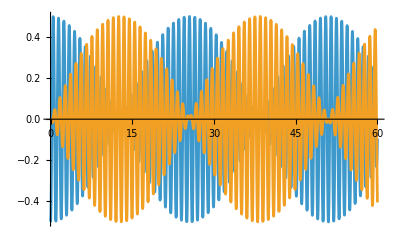

```mathematica
ListLinePlot[{timesAndx1s, timesAndx2s}]
```

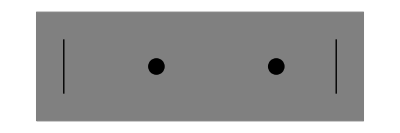

```mathematica
coupledOscillatorGraphic[x1_,x2_]:=Graphics[{
(* the first line makes a gray rectangle *)
{EdgeForm[Thin],Gray,Polygon[{{0,-1},{6,-1},{6,1},{0,1}}]},
Line[{{0.5,-0.5},{0.5,0.5}}],
Line[{{5.5,-0.5},{5.5,0.5}}],
Style[Point[{x1+2,0}],PointSize[0.03]],
Style[Point[{x2+4,0}],PointSize[0.03]]
}]
coupledOscillatorGraphic[0.2, 0.4]
```

#### Animating The Graphics

```mathematica
Animate[coupledOscillatorGraphic[x1s[[i]],x2s[[i]]],{i,1,steps,1}, DefaultDuration->tFinal-tInitial]
```